# First Steps with the LagrangeMesh Package

This notebook describes a step-by-step numerical solution of the Schrödinger equation associated with the Quartic Anharmonic Oscillator (QAO) potential, V(x)=1/2 x^2+g x^4, for two different coupling constants g=0, 1. The goal of this notebook is to guide the user to obtain highly accurate energy estimates for a concrete problem using the LagrangeMesh Package. The discussion here presented can be applied to systems of different nature.

## Installation

Once the file LagrangeMesh.wl is downloaded by the user, it is ready to be installed. Below, we describe two options for this purpose.

## Full Installation

In the Mathematica’s menu, go to File  -> Install.
   A window will prompt you for more information. Fill in as follows:
   
  i. Type of Item to Install -> Package
 ii. Source -> Select file LagrangeMesh.wl 
iii. Install Name -> LagrangeMesh
 iv. Click OK.

Once the installation is successful, the file LagrangeMesh.wl can be deleted. To load the package in a given NoteBook, type Needs[“LagrangeMesh`”] in the command line and evaluate the cell. Each time the kernel is restarted,  the package has to be loaded as indicated.

## Loading the Package Temporarily

This is a simple alternative that requires no full installation. Loading the package is achieved by evaluating <<”path/LagrangeMesh.wl” in the command line of the notebook we want to work with. The explicit form of path is found by evaluating the command NotebookDirectory[]. This option only works if the package and the notebook (in which we will perform calculations) are contained in the same directory. Each time the kernel is restarted, the package has to be loaded as indicated. In this case, the file LagrangeMesh.wl must not be deleted.

## Preliminaries

The basic definition that we need is the potential. Let us construct the function V(x) by evaluating the next line

```mathematica
V[x_]:=1/2 x^2+g x^4
```

Note that we have not assigned the value for the coupling constant g, we can do it later. Now, let us load all commands that the package provides. To do so, we evaluate

```mathematica
Needs["LagrangeMesh`"]
```

Once the package is loaded, we proceed to construct those Hermite meshes that we are going to use further down:

```mathematica
BuildMesh["Hermite",10]
BuildMesh["Hermite",50]
BuildMesh["Hermite",100]
BuildMesh["Hermite",10,WorkingPrecision->30]
BuildMesh["Hermite",50,WorkingPrecision->30]
BuildMesh["Hermite",100,WorkingPrecision->30]
BuildMesh["Hermite",200,WorkingPrecision->30]
```

Hermite_10_WP_MachinePrecision.dat

Hermite_50_WP_MachinePrecision.dat

Hermite_100_WP_MachinePrecision.dat

Hermite_10_WP_30.dat

Hermite_50_WP_30.dat

Hermite_100_WP_30.dat

Hermite_200_WP_30.dat

## g=0

## Eigenvalues

At g=0 the potential V(x) describes a harmonic oscillator. For this system, the spectrum is known in exact form. Let us compute the eigenvalues using LagMeshEigenvalues with  N=10 mesh points, and then compare with exact results. First, we focus on the first five eigenvalues.

```mathematica
g=0;
HO=LagMeshEigenvalues[V[x],{x,-∞,∞},5,10]
```

{0.5,1.5,2.5,3.5,4.5}

As output, we obtained an ordered list that contains the first five eigenvalues calculated with MachinePrecision. At first glance, they look equal to the exact eigenvalues (given by E_n=n+1/2, n=0,...4). We can  compare results in a more detailed way:

```mathematica
HO-{1/2,3/2,5/2,7/2,9/2}
```

{-4.44089×10^-16,-3.55271×10^-15,-8.88178×10^-16,5.77316×10^-15,2.66454×10^-15}

The accuracy in terms of deviation is consistent with Machine precision, which in my computer corresponds to almost  an arithmetic of 16 digits, as we can check by evaluating the following:

```mathematica
N[MachinePrecision]
```

15.9546

Keeping the number of mesh points fixed, more accurate estimates of the first eigenvalues  can be obtained if we increase WorkingPrecision. Instead of MachinePrecision, we use an arithmetic of 30 digits.

```mathematica
HO=LagMeshEigenvalues[V[x],{x,-∞,∞},5,10,WorkingPrecision->30]
```

{0.5,1.5,2.5,3.5,4.5}

Once again, let us compare with the exact spectrum

```mathematica
HO-{1/2,3/2,5/2,7/2,9/2}
```

{0.,0.,0.,0.,0.}

Note that the order in deviation is almost consistent with the WorkingPrecision.

## Eigenfunctions

Exact expressions for eigenfunctions are known at g=0. In particular,  we have the following normalized function for the ground state.

```mathematica
Subscript[ψ, 0][x_]:=1/π^(1/4)Exp[-1/2 x^2]
```

The ground state normalized eigenfunction can be calculated with MachinePrecision using the package, as shown below.

```mathematica
GS=LagMeshEigenfunctions[V[x],{x,-∞,∞},1,10]
```

ⅇ^(-x^2/2) (0.751126+6.21725×10^-15 x+1.53696×10^-15 x^2-2.66454×10^-15 x^3+1.59595×10^-16 x^4+1.66533×10^-16 x^5-5.89806×10^-17 x^6-6.93889×10^-17 x^7-3.46945×10^-18 x^8+1.73472×10^-18 x^9)

If we plot the absolute deviation between the exact and approximate solution as a function of x, it will give us an idea of the accuracy of the method. For this purpose, we have

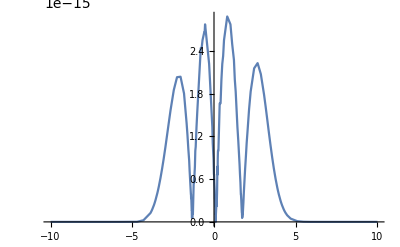

```mathematica
Plot[Abs[Subscript[ψ, 0][x]-GS],{x,-10,10}]
```

In this case, the order of the deviation is consistent with the requested accuracy. For for the harmonic oscillator, the LagrangeMesh method leads to the exact eigenvalues and eigenfunctions within the desired accuracy. Therefore, we can reduce the deviation using a larger value for WorkingPrecision in calculations.

## g=1

## Eigenvalues

At g=1 the potential V(x) admits no exact solutions. A natural question arises: how can we study the accuracy of our results?  We will focus the discussion on the ground state only. But similar considerations can be made for excited states. Firstly, we calculate the energy with N=10 mesh points and MachinePrecision. Gradually we will increase the value of N up to N=100 and modify WorkingPrecision accordingly.

```mathematica
g=1;
NumberForm[LagMeshEigenvalues[V[x],{x,-∞,∞},1,10],15]
NumberForm[LagMeshEigenvalues[V[x],{x,-∞,∞},1,50],15]
NumberForm[LagMeshEigenvalues[V[x],{x,-∞,∞},1,100],15]
```

0.805461942299127

0.803770651211246

0.803770654796773

Secondly, we consider the same mesh points, but with a higher value of WorkingPrecision and compare with previous results.

```mathematica
LagMeshEigenvalues[V[x],{x,-∞,∞},1,10,WorkingPrecision->30]
LagMeshEigenvalues[V[x],{x,-∞,∞},1,50,WorkingPrecision->30]
LagMeshEigenvalues[V[x],{x,-∞,∞},1,100,WorkingPrecision->30]
```

0.8054619422991244685221824196

0.803770651213375558760762106

0.80377065123427376830457827

Note that the estimates are similar, but they do not coincide in all displayed digits despite the fact the number of mesh points does. In this case, we observe that MachinePrecision is not enough to see the real scope of the LagMeshEigenvalues: numerical errors contaminate our calculations, especially for large meshes. Note that results for N=50 and N=100 mesh points predict the same energy within the first 11 decimal digits. As heuristic remarks about the QAO, the larger value of WorkingPrecision we use, the smaller numerical errors associated with  arithmetic operations are involved.  On the other hand, the larger the mesh, the more accurate results.

## Eigenfunctions

The ground state eigenfunction may be calculated through

```mathematica
AHOGS=LagMeshEigenfunctions[V[x],{x,-∞,∞},1,100,WorkingPrecision->30]
```

ⅇ^(-x^2/2) (-0.869276838869585465507387042435+0.264060791185154427587030115571 x^2+0.074651281568831780006251584477 x^4-0.0395565967242760304371627271079 x^6+0.00138354100754097614188603115686 x^8+0.00189546865507188079398060333177 x^10-0.000320891619893150317978032081463 x^12-0.0000258744711793566842664197511564 x^14+0.0000125863088775144498363726791387 x^16-5.71455526744021253375329388463×10^-7 x^18-3.40445715856127154374015035064×10^-7 x^20+9.86059686140278213839684922186×10^-8 x^22-2.20370445387909130751704083725×10^-8 x^24+5.78254919633129569058395211956×10^-9 x^26-1.44902341592203502516623647761×10^-9 x^28+2.92821329893087397112904626831×10^-10 x^30-4.67690059493389180680210511279×10^-11 x^32+6.02571529821800960040568181507×10^-12 x^34-6.40738965870837532341652601728×10^-13 x^36+5.7281075181028201279832475446×10^-14 x^38-4.36648573794079420879788281969×10^-15 x^40+2.86880926426008351638599012076×10^-16 x^42-1.6378956786321107607510954783×10^-17 x^44+8.17789827998808617496211324278×10^-19 x^46-3.58848023636509814220945903869×10^-20 x^48+1.38917841721877628231272328727×10^-21 x^50-4.75846103405833908785027236606×10^-23 x^52+1.4454433158884779049710144243×10^-24 x^54-3.89990724325444182001816182845×10^-26 x^56+9.35570024738014857594757720356×10^-28 x^58-1.99661054985841310111158662844×10^-29 x^60+3.79068011360360907845263769112×10^-31 x^62-6.39950098140890459264762971427×10^-33 x^64+9.59752950263847600274704324812×10^-35 x^66-1.27674216958758125118606367226×10^-36 x^68+1.50337656317116954442991009295×10^-38 x^70-1.56262642746961434255550722346×10^-40 x^72+1.42867306780147508148131108049×10^-42 x^74-1.14385242397300791704943117128×10^-44 x^76+7.97533015148384014677540173755×10^-47 x^78-4.80882516827132288876242563767×10^-49 x^80+2.48553141773558837888066799587×10^-51 x^82-1.08895315576633881321200710829×10^-53 x^84+3.9852739596770954474592980452×10^-56 x^86-1.19474800834943196581720085657×10^-58 x^88+2.85543388386854194731447792637×10^-61 x^90-5.2280463613057579742747095586×10^-64 x^92+6.88102814819279308298115574105×10^-67 x^94-5.7922532589985733906900321031×10^-70 x^96+2.34074021311572130921142200262×10^-73 x^98)

Let us plot the eigenfunction that we just constructed

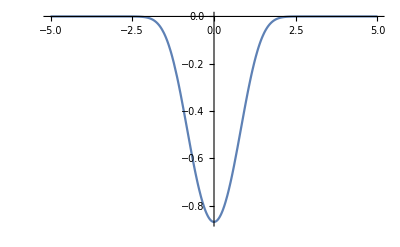

```mathematica
Plot[AHOGS,{x,-5,5}]
```

The plot shows that the approximate eigenfunction wave function is small ∼10^-7 for |x|>5. This can be checked numerically as follows.

```mathematica
AHOGS/.x->5
```

-2.195043297232×10^-7

Let us increase the domain in which we are plotting to see an interesting but not desired phenomenon.

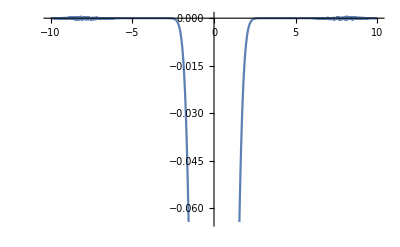

```mathematica
Plot[AHOGS,{x,-10,10}]
```

Non-physical rapid oscillations appear in the tales of the eigenfunction. This is a numerical artifact due to the accumulation of errors. We can get rid of them by increasing the value of WorkingPrecision, but the expression for the eigenfunction may  become extremely large. An alternative is using a discrete version of the eigenfunction,  free of those errors.

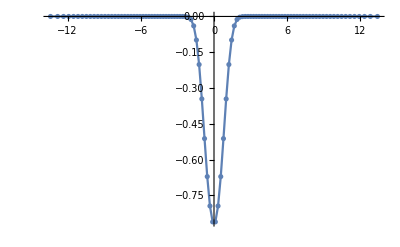

```mathematica
AHOGS=LagMeshEigenfunctions[V[x],{x,-∞,∞},1,100,WorkingPrecision->30,DiscreteFunction->True];
ListPlot[AHOGS,Joined->True,PlotRange->All,Mesh->All]
```

Using this DicreteFunction->True, we generate a list of pairs with a discrete version of the  eigenfunction on the mesh points. In fact, the plot shown above displays in the horizontal axis the distribution of the mesh points for N=100. According to it, they are contained in the interval -15 <x< 15 . We can be more precise about the interval if we use the following

```mathematica
AvailableMeshQ["Hermite",Dimension->100,WorkingPrecision->30,PrintDomain->True]
```

{-13.4065,13.4065}

So, mesh points are contained  in [-13.41,13.41]. Moving mesh points to regions where the eigenfunction is not extremely small can be of benefit in terms of accuracy and  performance of the package. In the present case, we previously established that the  eigenfunction is not small inside [-5,5]. We can move the mesh points to such region via Scaling(which by default is set to Scaling->1). In this case, Scaling->1/2 seems to be appropriate to get rid of those oscillatory tails. Let us check this statement with the following lines of code.

√2 ⅇ^(-2 x^2) (-0.614671547494819507503853088586-0.735288144964549099987528576733 x^2-0.358640302051891327715006866582 x^4-0.0844847565370426542117265349815 x^6-0.00622082791990447499984233396173 x^8+0.00152194092461276165835126318725 x^10+0.00037681333708881571710637080458 x^12+9.91659888559748053706090426256×10^-6 x^14-6.14139199426298140844878178522×10^-6 x^16-6.4024023263203156346355697092×10^-7 x^18+4.79677266773106611430499413018×10^-8 x^20+1.106150676225903586868959394×10^-8 x^22+7.81230511298488848412014918009×10^-58 x^98)

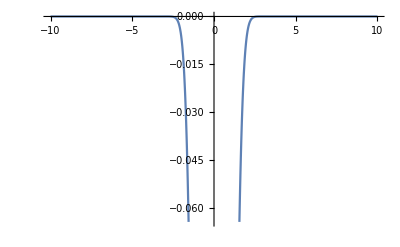

```mathematica
AHOGS=LagMeshEigenfunctions[V[x],{x,-∞,∞},1,100,WorkingPrecision->30,Scaling->1/2]
Plot[AHOGS,{x,-10,10}]
```

Rapid Oscillatory tails are gone. Now we have found an appropriate value for Scaling, we can return to the evaluation of the energy to see the effect of Scaling.

```mathematica
(* Without Scaling *)
EwtS=LagMeshEigenvalues[V[x],{x,-∞,∞},1,100,WorkingPrecision->30]
(* With Scaling *)
EwS=LagMeshEigenvalues[V[x],{x,-∞,∞},1,100,WorkingPrecision->30,Scaling->1/2]
```

0.80377065123427376830457827

0.80377065123427376935408596

```mathematica
EwtS-EwS
```

-1.0495077×10^-18

According to the difference, they deviate each other in the 18th decimal place. The question is, which one is better? To answer the question, we can consider a larger mesh in calculations, say N=200. Below, we use Method->”Arnoldi”  to reduce CPU times.

```mathematica
E200=LagMeshEigenvalues[V[x],{x,-∞,∞},1,200,WorkingPrecision->30,Method->"Arnoldi"]
```

0.803770651234273769354086

Note that LagMeshEigenvalues with  N=100 mesh points and Scaling ->1/2 can achieve the results of 200! (It is important to mention that numerically convergence has been demonstrated once N increases for Scaling ->1, see text ).